```mathematica
<< xAct`xCoba`
```

------------------------------------------------------------

Package xAct`xPerm`  version 1.2.3, {2015,8,23}

CopyRight (C) 2003-2020, Jose M. Martin-Garcia, under the General Public License.

Connecting to external MinGW executable...

Connection established.

------------------------------------------------------------

Package xAct`xTensor`  version 1.2.0, {2021,10,17}

CopyRight (C) 2002-2021, Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

Package xAct`xCoba`  version 0.8.6, {2021,2,28}

CopyRight (C) 2005-2021, David Yllanes and Jose M. Martin-Garcia, under the General Public License.

------------------------------------------------------------

These packages come with ABSOLUTELY NO WARRANTY; for details type Disclaimer[]. This is free software, and you are welcome to redistribute it under certain conditions. See the General Public License for details.

------------------------------------------------------------

```mathematica
DefManifold[M,4,IndexRange[a,q]];
DefChart[ch,M,{0,1,2,3},{t[],r[],θ[],ϕ[]},ChartColor -> Blue];
DefConstantSymbol[mass, PrintAs-> "M"];
```

** DefManifold: Defining manifold M.

** DefVBundle: Defining vbundle TangentM.

** DefChart: Defining chart ch.

** DefTensor: Defining coordinate scalar t[].

** DefTensor: Defining coordinate scalar r[].

** DefTensor: Defining coordinate scalar θ[].

** DefTensor: Defining coordinate scalar ϕ[].

** DefMapping: Defining mapping ch.

** DefMapping: Defining inverse mapping ich.

** DefTensor: Defining mapping differential tensor dich[-a,icha].

** DefTensor: Defining mapping differential tensor dch[-a,cha].

** DefBasis: Defining basis ch. Coordinated basis.

** DefCovD: Defining parallel derivative PDch[-a].

** DefTensor: Defining vanishing torsion tensor TorsionPDch[a,-b,-c].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch[a,-b,-c].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch[-a,-b,-c,d].

** DefTensor: Defining vanishing Ricci tensor RicciPDch[-a,-b].

** DefTensor: Defining antisymmetric +1 density etaUpch[a,b,c,d].

** DefTensor: Defining antisymmetric -1 density etaDownch[-a,-b,-c,-d].

** DefConstantSymbol: Defining constant symbol mass.

```mathematica
$Assumptions = mass >0 && r[] > 2 mass && 0 < θ[]<π && 0< ϕ[]< 2π && t[]∈Reals; 
gg=CTensor[{{-Exp[-2mass/r[]],0,0,0},{0,Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2],0,0},{0,0,Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2]r[]^2,0},{0,0,0,Exp[2mass/r[]]r[]^2 Sin[θ[]]^2}},{-ch,-ch}];
SetCMetric[gg,ch,SignatureOfMetric->{3,1,0}];
cd=CovDOfMetric[gg];

gmatrix= ComponentArray[gg[{-a,-ch},{-b,-ch}]] // MatrixForm;
```

```mathematica
gg[-a,-b]
```

-ⅇ^(-(2 M)/r) | 0 | 0 | 0
0 | ⅇ^((2 M)/r-(M^2 Sin[θ]^2)/r^2) | 0 | 0
0 | 0 | ⅇ^((2 M)/r-(M^2 Sin[θ]^2)/r^2) r^2 | 0
0 | 0 | 0 | ⅇ^((2 M)/r) r^2 Sin[θ]^2 |   |  
a | b

```mathematica
weyl=Weyl[cd][{-a,-ch},{-b,-ch},{-c,-ch},{-d,-ch}];
```

```mathematica
(*La base tetrada*)
l=CTensor[{Exp[-mass/r[]]/Sqrt[2],(Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2])^(1/2)/Sqrt[2],0,0},{-ch}];
n=CTensor[{Exp[-mass/r[]]/Sqrt[2],-(Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2])^(1/2)/Sqrt[2],0,0},{-ch}];
m=CTensor[{0,0,(Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2]r[]^2)^(1/2)/Sqrt[2],I Exp[mass/r[]]Sin[θ[]] r[]/Sqrt[2]},{-ch}];
mb=CTensor[{0,0,(Exp[2mass/r[]]Exp[-(mass^2 Sin[θ[]]^2)/r[]^2]r[]^2)^(1/2)/Sqrt[2],-I Exp[mass/r[]]Sin[θ[]] r[]/Sqrt[2]},{-ch}];
```

```mathematica
mb[a]mb[-a]//FullSimplify
```

0

```mathematica
(*Se define el Killing*)
k=CTensor[{1,0,0,0},{ch}];

F= cd[-a]@k[-b]//Simplify;
F=Head[F];
Fd= F[-a,-b]+I/2 epsilon[gg][-a,-b,e,f]F[-e,-f];
Fd= Head[Fd];
```

```mathematica
σ= 2Fd[-a,-b]k[b]//FullSimplify;
σ=Head[σ];
```

```mathematica
σ[a]
```

0
(2 ⅇ^((M (-4 r+M Sin[θ]^2))/r^2) M)/r^2
0
0 | a

```mathematica
DefScalarFunction[sg];
```

** DefScalarFunction: Defining scalar function sg.

```mathematica
cd[-a]@sg[r[],θ[]]==σ[-a]//FullSimplify
```

e |   | 2
a |   sg^(0,1)[r,θ]+e |   | 1
a |   sg^(1,0)[r,θ]==0
(2 ⅇ^(-(2 M)/r) M)/r^2
0
0 |  
a

```mathematica
DSolve[sg'[r[]]==-2mass Exp[-2mass/r[]]/r[]^2,{sg[r[]]},{r[]}]
```

Attributes::notfound: Symbol DSolveDispatchODE not found.

{{sg[r]→-ⅇ^(-(2 M)/r)+C[1]}}

```mathematica
σE= 1- Exp[-2mass/r[]];
```

```mathematica
(*Componentes del tensor de Weyl*)
ps0= -Weyl[cd][-a,-b,-c,-d]l[a]m[b]l[c]m[d]// Simplify;
ps1= -Weyl[cd][-a,-b,-c,-d]l[a]n[b]l[c]m[d]// Simplify;
ps2= 1/2 Weyl[cd][-a,-b,-c,-d](l[a]n[b]l[c]n[d]+l[a]n[b]m[c]mb[d])// Simplify;
ps3= Weyl[cd][-a,-b,-c,-d]l[a]n[b]n[c]mb[d]// Simplify;
ps4= -Weyl[cd][-a,-b,-c,-d]n[a]mb[b]n[c]mb[d]// Simplify;
```

```mathematica
ps4
```

-(ⅇ^((M (-2 r+M Sin[θ]^2))/r^2) M^3 Sin[θ]^2)/(2 r^5)

```mathematica
(*Definos las matrices alpha*)
α1=m[-a]mb[-b]-mb[-a]m[-b]+l[-a]n[-b]-n[-a]l[-b] // Simplify;
α2= -l[-a] mb[-b]+mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b] // Simplify;
α3= I(l[-a] mb[-b]-mb[-a] l[-b]+m[-a] n[-b]-n[-a] m[-b])// Simplify;
```

```mathematica
DefManifold[S3,3,{P,Q,S,R,T}];
DefChart[ch3,S3,{0,1,2},{u[],v[],w[]},ChartColor -> Red];


(*Métrica δ_ij=identidad 3x3*)
g3=CTensor[{{1,0,0},{0,1,0},{0,0,1}},{-ch3,-ch3}];
SetCMetric[g3,ch3,SignatureOfMetric->{0,3,0}];
cd3=CovDOfMetric[g3];

g3matrix= ComponentArray[g3[{-P,-ch3},{-Q,-ch3}]] // MatrixForm;
```

** DefManifold: Defining manifold S3.

** DefVBundle: Defining vbundle TangentS3.

** DefChart: Defining chart ch3.

** DefTensor: Defining coordinate scalar u[].

** DefTensor: Defining coordinate scalar v[].

** DefTensor: Defining coordinate scalar w[].

** DefMapping: Defining mapping ch3.

** DefMapping: Defining inverse mapping ich3.

** DefTensor: Defining mapping differential tensor dich3[-e,ich3P].

** DefTensor: Defining mapping differential tensor dch3[-P,ch3e].

** DefBasis: Defining basis ch3. Coordinated basis.

** DefCovD: Defining parallel derivative PDch3[-P].

** DefTensor: Defining vanishing torsion tensor TorsionPDch3[P,-Q,-R].

** DefTensor: Defining symmetric Christoffel tensor ChristoffelPDch3[P,-Q,-R].

** DefTensor: Defining vanishing Riemann tensor RiemannPDch3[-P,-Q,-R,S].

** DefTensor: Defining vanishing Ricci tensor RicciPDch3[-P,-Q].

** DefTensor: Defining antisymmetric +1 density etaUpch3[P,Q,R].

** DefTensor: Defining antisymmetric -1 density etaDownch3[-P,-Q,-R].

```mathematica
Head[α3]
```

CTensor[{{0,0,0,r Sin[θ]},{0,0,ⅈ ⅇ^(-(M (-2 r+M Sin[θ]^2))/r^2) r,0},{0,-ⅈ ⅇ^(-(M (-2 r+M Sin[θ]^2))/r^2) r,0,0},{-r Sin[θ],0,0,0}},{-ch,-ch},0]

```mathematica
(*Se crea ya si con los índices internos IJ en la subvariedad*)
Alpha=CTensor[{{{0,-ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)),0,0},{ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)),0,0,0},{0,0,0,-ⅈ ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r^2 Sin[θ]},{0,0,ⅈ ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r^2 Sin[θ],0}},{{0,0,-ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r,0},{0,0,0,ⅈ ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r Sin[θ]},{ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r,0,0,0},{0,-ⅈ ⅇ^(-(M (-4 r+M Sin[θ]^2))/(2 r^2)) r Sin[θ],0,0}},{{0,0,0,ⅇ^((2 M)/r) r Sin[θ]},{0,0,ⅈ ⅇ^(-(M (-2 r+M Sin[θ]^2))/r^2) r,0},{0,-ⅈ ⅇ^(-(M (-2 r+M Sin[θ]^2))/r^2) r,0,0},{-ⅇ^((2 M)/r) r Sin[θ],0,0,0}}},{ch3,-ch,-ch}];
```

```mathematica
(*Se define la matriz H_IJ*)

H= CTensor[{{4ps2,0,0},{0,-2ps2,0},{0,0,-2ps2}},{-ch3,-ch3}];
```

```mathematica
FI=Alpha[P,-a,-b]k[b]σ[a]//Simplify;
FI=Head[FI];
```

```mathematica
fff=FI[P]FI[-P]
```

(4 ⅇ^((M (-4 r+M Sin[θ]^2))/r^2) M^2)/r^4

```mathematica
Fd[-a,-b]Fd[a,b]//Simplify
```

-(4 ⅇ^((M (-4 r+M Sin[θ]^2))/r^2) M^2)/r^4

```mathematica
ve=CTensor[{1,0,0},{ch3}];
```

```mathematica
fff=3/8(Alpha[P,-a,-b]Fd[a,b]ve[-P]Alpha[P,-a,-b]Fd[a,b]ve[-P]-4/3Fd[-a,-b]Fd[a,b])//FullSimplify
```

(ⅇ^((M (-4 r+M Sin[θ]^2))/r^2) (7-6 ⅇ^((2 M)/r)+3 ⅇ^((4 M)/r)) M^2)/(2 r^4)

```mathematica
ps2
```

-(ⅇ^((M (-2 r+M Sin[θ]^2))/r^2) M (2 r (-M+r)+M^2 Sin[θ]^2))/(2 r^5)

```mathematica
L= ps2/fff/.θ[]->0//Simplify
```

(2 ⅇ^((2 M)/r) (M-r))/((7-6 ⅇ^((2 M)/r)+3 ⅇ^((4 M)/r)) M)

```mathematica
-1/σE
```

-1/(1-ⅇ^(-(2 M)/r))

```mathematica
q=Abs[L+1/σE]^2/ (Abs[L]+Abs[1/σE])^2/.mass->12//Simplify
```

Piecewise[{{1, (12-r)/(7-6 ⅇ^(24/r)+3 ⅇ^(48/r))≥0}, {((30+18 ⅇ^(48/r)+r-ⅇ^(24/r) (24+r))^2)/((54+18 ⅇ^(48/r)+ⅇ^(24/r) (-48+r)-r)^2), True}}]

```mathematica
Numerator[q]
```

Piecewise[{{1, (12-r)/(7-6 ⅇ^(24/r)+3 ⅇ^(48/r))≥0}, {((30+18 ⅇ^(48/r)+r-ⅇ^(24/r) (24+r))^2)/((54+18 ⅇ^(48/r)+ⅇ^(24/r) (-48+r)-r)^2), True}}]

```mathematica
r[]-> 2(1+r[]Exp[r[]/2-1])
```

r→2 (1+ⅇ^(-1+r/2) r)

General::munfl: 11.998 1.3214970359×10^-10205 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 11.998 (-1.3214970359×10^-10205) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

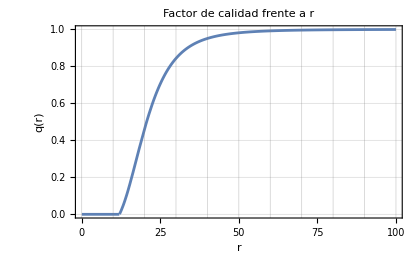

```mathematica
grafica=Plot[1-q,{r,0,100},Frame->True,PlotLabel->"Factor de calidad frente a r",FrameLabel->{"r","q(r)"},Ticks->{Table[i,{i,0,100,10}],Automatic},GridLines->{Table[i,{i,0,100,10}],Automatic}]
```

```mathematica
Export["miGrafico.png",grafica];
```

```mathematica
SystemOpen["miGrafico.png"]
```

```mathematica
6L(FI[-P]FI[-Q]-1/3 FI[S]FI[-S]g3[-P,-Q])==  H[-P,-Q]
```

● | 0 | 0
0 | ● | 0
0 | 0 | ● |   |  
P | Q==● | 0 | 0
0 | ● | 0
0 | 0 | ● |   |  
P | Q

```mathematica
H[-P,-Q]
```

● | 0 | 0
0 | ● | 0
0 | 0 | ● |   |  
P | Q

```mathematica
cd[-b]@k[-a]+cd[-a]@k[-b]//Simplify
```

0

```mathematica
L=4ps2/fff//FullSimplify
```

(-M^2 Cos[2 θ]+(M-2 r)^2)/(M r (3-5 Cosh[(2 M)/r]+2 Sinh[(2 M)/r]))

```mathematica
-1/σE
```

-1/(1-ⅇ^(-(2 M)/r))

```mathematica
HC=Dagger[H[R,S]]
```

● | 0 | 0
0 | ● | 0
0 | 0 | ● | R | S
  |

```mathematica
Cad=H[R,S]Alpha[-R,-a,-b]Alpha[-S,-c,-d];
Cad=Head[Cad];
```

```mathematica
UC= H[P,Q]Dagger[H[R,S]](Alpha[-P,-c,-e]Alpha[-Q,-d,-f]Dagger [Alpha[-R,-a,e]]Dagger[Alpha[-S,-b,f]])k[a]k[b]k[c]k[d]//FullSimplify
```

(6 ⅇ^((2 M^2 Sin[θ]^2)/r^2) (2 M r (-M+r)+M^3 Sin[θ]^2)^2)/r^10

```mathematica
II=1/4(gg[-a,-c]gg[-b,-d]-gg[-a,-d]gg[-b,-c]+I epsilon[gg][-a,-b,-c,-d]);
```

```mathematica
II=Head[II];
```

```mathematica
Q=6(Fd[-a,-b]Fd[-c,-d]-II[-a,-b,-c,-d]Fd[e,f]Fd[-e,-f]/3);
```

```mathematica
Q=Head[Q];
```

```mathematica
Qd= 1/2epsilon[gg][-a,-b,e,f]Q[-e,-f,-c,-d];
Qd=Head[Qd];
```

```mathematica
UQ=1/2(Q[-a,-e,-b,-f]Q[-c,e,-d,f]+Qd[-a,-e,-b,-f]Qd[-c,e,-d,f])k[a]k[b]k[c]k[d]//FullSimplify
```

0

```mathematica
weyl=Weyl[cd][-a,-b,-c,-d];
weyld= 1/2epsilon[gg][-a,-b,e,f]Weyl[cd][-e,-f,-c,-d];
weyld=Head[weyld];
```

```mathematica
Cad=1/2(weyl[-a,-b,-c,-d]-I weyld[-a,-b,-c,-d]);
Cad=Head[Cad];
```

```mathematica
SS=Cad[-a,-b,-c,-d]+6(Fd[-a,-b]Fd[-c,-d]-II[-a,-b,-c,-d]Fd[e,f]Fd[-e,-f]/3);
SS=Head[SS];
```

```mathematica
SS[-a,-b,-c,-d]
```

-a-b-c-d

```mathematica
SSd= 1/2epsilon[gg][-a,-b,e,f]SS[-e,-f,-c,-d];
SSd=Head[SSd];
```

```mathematica
US=1/2(SS[-a,-e,-b,-f]SS[-c,e,-d,f]+SSd[-a,-e,-b,-f]SSd[-c,e,-d,f])k[a]k[b]k[c]k[d]//FullSimplify
```

(a b c d e^2 f^2+(c+d-e-f) (a+b+e+f)) 1/2 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | b | c | d
  |   |   |

```mathematica
QQ=US/(Sqrt[UC]+Sqrt[UQ]/Abs[σE])^2/.mass->12//Simplify
```

(a b c d e^2 f^2+(c+d-e-f) (a+b+e+f)) ● | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0 | a | b | c | d
  |   |   |